Definition of RK4

```mathematica
crkamat={{1/2},{0,1/2},{0,0,1}};
crkbvec={1/6,1/3,1/3,1/6};
crkcvec={1/2,1/2,1};
ClassicalRungeKuttaCoefficients[4,p_]:=N[{crkamat,crkbvec,crkcvec},p];
```

Compile the NDSolve parameter sweep

```mathematica
logistic1=Compile[
{{parameterList,_Real,1}},
Table[
sol=NDSolve[
{
x'[t] == x[t]*(parameterList[[i]]- x[t-1]),
x[t/;t≤0] ==1.5-Cos[t]
},
x[t],
{t,0,10},
Method->{"ExplicitRungeKutta","DifferenceOrder"->4,"Coefficients"->ClassicalRungeKuttaCoefficients},
StartingStepSize->0.001,
MaxSteps->10100
];
First@Evaluate[x[t]/.sol]/.t->10,
{i,1,Length[parameterList]}],
CompilationTarget->"C",
"RuntimeOptions"->"Speed"
]
```

CompiledFunction[…]

Run and Benchmark

```mathematica
nrOfParameters = 128;
parameterList =N@Range[0,4,4/(nrOfParameters-1)];
runtime=Timing[endvals=logistic1[parameterList]];
runtime[[1]]
```

30.25

Export endvals

```mathematica
SetDirectory[NotebookDirectory[]];
Export["logistic1_endvals.txt",data=Transpose[{parameterList,endvals}],"Table"]
```

logistic1_endvals.txt

Plot endvals

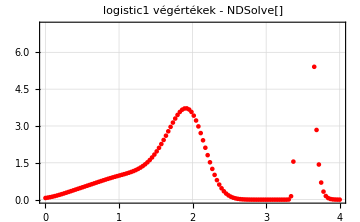

logistic1_endvals.png

```mathematica
plt=Show[
(*Plot[Evaluate[x[p][10]/.logistic1EndValues],{p,0,2},PlotStyle->Blue],*)
ListPlot[
data[[All,{1,2}]],
PlotStyle->Red,
FrameLabel->(MaTeX[#,Magnification->1.2]&)/@{"p","x(10)"},
PlotLabel->Style["logistic1 végértékek - NDSolve[]",Black,14]
]
]
Export["logistic1_endvals.png",plt,ImageResolution->1000]
```